```mathematica
Guy F. Mongelli                                                                             ECHE 462;
Prof. R.M. Sankaran                                                                  1/25/2013;
```

```mathematica
Problem Set #2;
```

```mathematica
Needs["PlotLegends`"];
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
Clear[cA,cB,cC]
```

```mathematica
Exercise 1:
```

```mathematica
A+B↔C
```

A+B↔C

```mathematica
Assumptions:
1)Temperature is constant (300K)
         2)Volume is constant (1.0L)
```

```mathematica
Since volume is constant, the concentration of each species can be easily converted to moles.  However, this problem will be solved in concentration due to the simplification of 1.0 L.
```

```mathematica
Initial moles:
```

```mathematica
nA0=1.0 (* moles *);
```

```mathematica
nB0=2.0(* moles *);
```

```mathematica
nC0=0.0(* moles *);
```

```mathematica
Initial concentrations:
```

```mathematica
cA0=1.0 (* moles/L *);
```

```mathematica
cB0=2.0(* moles/L *);
```

```mathematica
cC0=0.0(* moles/L *);
```

```mathematica
Rate constants:
```

```mathematica
k1=6.0 (* L/mol-hr *);
```

```mathematica
k2=3.0 (* h^-1 *);
```

```mathematica
The eqilibrium constant is then:
```

```mathematica
keq=k1/k2
```

2.

```mathematica
Eliminating cB and cC:
```

```mathematica
cB[t_]=cB0-(cA0-cA[t])
```

1.+cA[t]

```mathematica
cC[t_]=cC0+(cA0-cA[t])
```

1.-cA[t]

```mathematica
The right hand side of the rate equation is then:
```

```mathematica
-k1*cA[t]*cB[t]+k2*cC[t]
```

3. (1.-cA[t])-6. cA[t] (1.+cA[t])

```mathematica
Collecting terms:
```

```mathematica
Simplify[-k1*cA[t]*cB[t]+k2*cC[t]]
```

3.-9. cA[t]-6. cA[t]^2

```mathematica
Rearranging:
```

```mathematica
dcA/(3.-9. cA[t]-6. cA[t]^2)=1dt;
```

Set::write: Tag Times in dcA/3.  - 9.\ cA[t] - 6.\ cA[t]^2 is Protected.

```mathematica
Then, utilize Mathematica's DSolve function to obtain the following solution:
```

```mathematica
DSolve[{ca'[t]==-k1*ca[t](cB0-(cA0-ca[t]))+k2*(cA0-ca[t]),ca[0]==cA0},ca[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ca[t]→(0.280776 ((1.64039+5.27589×10^-16 ⅈ)+1. 2.71828^(12.3693 t)))/((-0.258641-8.31854×10^-17 ⅈ)+2.71828^(12.3693 t))}}

```mathematica
For some reason, Mathematica is providing a complex solution, likely because it accounts for negative time.  It is negligible since the complex coefficients are negligible compared to the rest of the terms (10^-16) and can be neglected.  This shows that Mathematica does not always provide the exact and relevant engineering solution to a problem, but the mathematically correct one.  To simplify, we take only the real part of the solution which is valid for t>=0.
```

```mathematica
f[t_]=Re[(0.28077640640441515 ((1.6403882032022072+5.275890847663661*^-16 ⅈ)+1. 2.718281828459045^(12.36931687685298 t)))/((-0.2586412887922735-8.31853829296822*^-17 ⅈ)+2.718281828459045^(12.36931687685298 t))]
```

0.280776 Re[((1.64039+5.27589×10^-16 ⅈ)+1. 2.71828^(12.3693 t))/((-0.258641-8.31854×10^-17 ⅈ)+2.71828^(12.3693 t))]

```mathematica
f[.00001]
```

0.99988

```mathematica
Needs["PlotLegends`"]
```

```mathematica
Plot[{f[t],cB0-(cA0-f[t]),(cA0-f[t])},{t,0,2},PlotLegend->{"cA[t]","cB[t]","cC[t]"},AxesLabel->{"time(hrs)","Concentration(mol/L)"}]
```

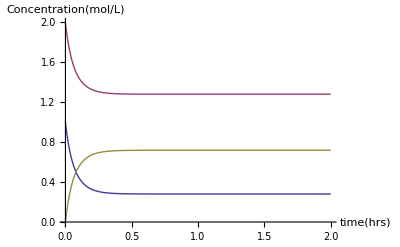

```mathematica
In the infinite limit (t=1 is close enough), equilibrium is reached and the concentration of reactant A (moles/L)is:
```

```mathematica
Limit[f[t],t->1]
```

0.280779

```mathematica
In the infinite limit, equilibrium is reached and the concentration of reactant B (moles/L)is:
```

```mathematica
Limit[cB0-(cA0-f[t]),t->1]
```

1.28078

```mathematica
In the infinite limit, equilibrium is reached and the concentration of reactant C (moles/L)is:
```

```mathematica
Limit[(cA0-f[t]),t->1]
```

0.719221

```mathematica
As a quick check, triple the time and observe a negligible concentration change:
```

```mathematica
Limit[f[t],t->3]
```

0.280776

```mathematica
Limit[cB0-(cA0-f[t]),t->3]
```

1.28078

```mathematica
Limit[(cA0-f[t]),t->3]
```

0.719224

```mathematica
The pressure of the system will depend on the number of moles present:
```

```mathematica
n[t_]=f[t]+cB0-(cA0-f[t])+(cA0-f[t])
```

2.+0.280776 Re[((1.64039+5.27589×10^-16 ⅈ)+1. 2.71828^(12.3693 t))/((-0.258641-8.31854×10^-17 ⅈ)+2.71828^(12.3693 t))]

```mathematica
The following lines of code evaluate the number of moles of gas at 0 hours,1 hour and 3 hours.
```

```mathematica
n[0]
```

3.

```mathematica
n[1]
```

2.28078

```mathematica
n[3]
```

2.28078

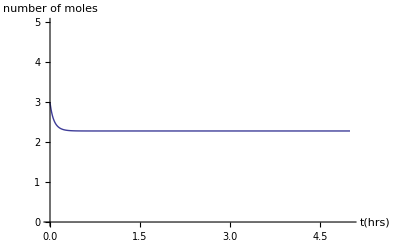

```mathematica
Plot[n[t],{t,0,5},PlotRange->{0,5},AxesLabel->{"t(hrs)","number of moles"}]
```

```mathematica
A direct method to determine equilibrium concentrations without using rate equations was utilized in assignment one.  Recall to treat this as an ICE problem.
```

```mathematica
{{I, 1, 2, 0}, {C, -x, -x, +x}, {E, 1-x, 2-x, x}}
```

```mathematica
Keq=k1/k2
```

2.

```mathematica
Solve[2==x/((1-x)(2-x)),x]
```

{{x→1/4 (7-√17)},{x→1/4 (7+√17)}}

```mathematica
N[1/4 (7-√17),3]
```

0.719

```mathematica
Ignore the following root, since it is greater than one and has no physical meaning.
```

```mathematica
N[1/4 (7+√17),3]
```

2.78

```mathematica
The final number of moles will involve calculating the number of moles as a function of extent of reaction and evaluating the extent of reaction at the equilibrium value.
```

```mathematica
nmol[x_]=1-x+2-x+x
```

3-x

```mathematica
Therefore there are 2.281 moles at equilibrium:
```

```mathematica
nmol[.719]
```

2.281

```mathematica
PV=nRT
```

```mathematica
P=n*R*T/V
```

```mathematica
P=(2.281 (* moles *))*(0.082057 (* L*atm/mol-K *))*(300 (* K *))/(1 (* L *))
```

```mathematica
56.151605100000005
```

```mathematica
The above result is in atmospheres.
```

```mathematica
We can also plot the pressure in the system as a function of time.
```

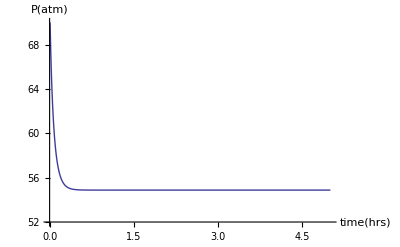

```mathematica
Plot[n[t]*.080205*300,{t,0,5},PlotRange->{52,70},AxesLabel->{"time(hrs)","P(atm)"}]
```

```mathematica
Problem 2:
```

```mathematica
In this case the concentration is a function of extent of reaction,as before, however it it slightly more complex since the volume is changing as a function of extent of reaction.  This can be accounted for by writing the number of moles as a function of extent of reaction and then writing the volume as a function of extent of reactin (invoking the ideal gas law along the way).
```

```mathematica
Many of the same variables from problem one are recorded here:
```

```mathematica
Initial moles:
```

```mathematica
nA0=1.0 (* moles *);
```

```mathematica
nB0=2.0(* moles *);
```

```mathematica
nC0=0.0(* moles *);
```

```mathematica
Initial concentrations:
```

```mathematica
cA0=1.0 (* moles/L *);
```

```mathematica
cB0=2.0(* moles/L *);
```

```mathematica
cC0=0.0(* moles/L *);
```

```mathematica
Rate constants:
```

```mathematica
k1=6.0 (* L/mol-hr *);
```

```mathematica
k2=3.0 (* h^-1 *);
```

```mathematica
The eqilibrium constant is then:
```

```mathematica
keq=k1/k2
```

2.

```mathematica
Eliminating cB and cC as before:
```

```mathematica
cB[t_]=cB0-(cA0-cA[t])
```

1.+cA[t]

```mathematica
cC[t_]=cC0+(cA0-cA[t])
```

1.-cA[t]

```mathematica
The right hand side of the rate equation is then:
```

```mathematica
-k1*cA[t]*cB[t]+k2*cC[t]
```

3. (1.-cA[t])-6. cA[t] (1.+cA[t])

```mathematica
Collecting terms:
```

```mathematica
Simplify[-k1*cA[t]*cB[t]+k2*cC[t]]
```

3.-9. cA[t]-6. cA[t]^2

```mathematica
Then cA[t] undergoes a change of variables to become cA[x]:
```

```mathematica
Simplify[-k1*cA[x]*cB[x]+k2*cC[x]]
```

3.-9. cA[x]-6. cA[x]^2

```mathematica
Susbstituting for cA[x]
```

```mathematica
Simplify[3.-9. ((1-x)/((1/3)(3-x)))-6.( ((1-x)/((1/3)(3-x))))^2]
```

(-108.+198. x-78. x^2)/(-3.+x)^2

```mathematica
Clear[P]
```

```mathematica
PV=n*R*T
```

```mathematica
First, calculate the initial pressure:
```

```mathematica
P0=N[3*.0802057*300 (* atm *),3]
```

72.1851

```mathematica
P*V=(3-x)*R*T
```

```mathematica
Rearranging, the volume as a function of extent of reaction is computed:
```

```mathematica
V[x_]=((3-x).0802057*300)/72.1851
```

0.333333 (3-x)

```mathematica
V[x_]=(3-x)/3
```

(3-x)/3

```mathematica
Note: Unless V[x]is redefined as in the line above (1/3) instead of .333, significant error is propagated into the concentration of the system.
```

```mathematica
0.33333 (3-x)
```

```mathematica
The ICE table for moles is the same as Problem one, except the number of moles of each species must be divided by the volume as a function of extent of reaction to get concentration.  Concentration must appear in the equilibrium expression.
```

```mathematica
Again:
```

```mathematica
Solve[(k1/k2)==(x/((3-x)/3))/(((cA0-x)/((3-x)/3))((cB0-x)/((3-x)/3))),x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.768075},{x→2.23193}}

```mathematica
cAeq=0.7681
```

```mathematica
1-xeq
```

0.232

```mathematica
xeq=0.768;
```

```mathematica
The following line of code is to double-check Mathematica's solution since it gave a warning.
```

```mathematica
NSolve[k1/k2==(x/((3-x)/3))/(((cA0-x)/((3-x)/3))((cB0-x)/((3-x)/3))),x]
```

{{x→2.23193},{x→0.768075}}

```mathematica
Therefore the equilibrium conversion is approx. .76 and is only slightly higher than in the isobaric case than in the isochoric case.
```

```mathematica
The volume at equlibrium is therefore:
```

```mathematica
V[.857] (* Liters *)
```

0.714333

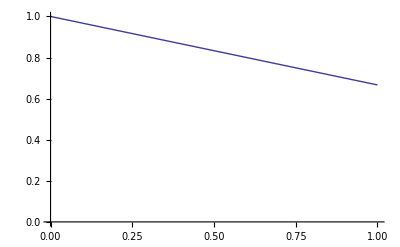

```mathematica
Plot[V[x],{x,0,1},PlotRange->{0,1}]
```

```mathematica
The next step is to write out the relevant differential rate equation.
```

```mathematica
Element[x[t],Reals];
```

```mathematica
DSolve[{D[(1-x[t])/((1/3)(3-x[t])),t]==-k1*((1-x[t])/((1/3)(3-x[t])))(cB0-(cA0-((1-x[t])/((1/3)(3-x[t])))))+k2*(cA0-((1-x[t])/((1/3)(3-x[t])))),x[0]==0},x[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x[t]→(0.793488 (2.19912-(2.19912-2.69314×10^-16 ⅈ) 2.71828^(12.3693 t)))/(1.-(2.19912-2.69314×10^-16 ⅈ) 2.71828^(12.3693 t))}}

```mathematica
FullSimplify[D[(1-x[t])/((1/3)*(3-x[t])),t]]
```

```mathematica
-(6 x'[t])/(-3+x[t])^2
```

```mathematica
Solve[-(6 x'[t])/(-3+x[t])^2==-k1*((1-x[t])/((1/3)(3-x[t])))(cB0-(cA0-(1-x[t])/((1/3)(3-x[t]))))+k2*(cA0-(1-x[t])/((1/3)(3-x[t]))),x'[t]]
```

{{x'[t]→-0.166667 (3. (1.-(3. (1.-1. x[t]))/(3.-1. x[t]))-(18. (1.+(3. (1.-1. x[t]))/(3.-1. x[t])) (1.-1. x[t]))/(3.-1. x[t])) (-3.+x[t])^2}}

```mathematica
∫_0^X 1/((3. (1.-(3. (1.-1. x))/(3.-1. x))-(18. (1.+(3. (1.-1. x))/(3.-1. x)) (1.-1. x))/(3.-1. x)) (-3.+x)^2)ⅆx
```

ConditionalExpression[-0.0128205 (-0.828238-1.05099 Log[0.793488-1. X]+1.05099 Log[1.74497-1. X]),(Re[X]<0.793488&&Re[X]>0&&(Re[1/X]>1.26026||1/X∉Reals))||((Re[X]<0||X∉Reals)&&(Re[1/X]≥1.26026||Re[1/X]≤0||1/X∉Reals))]

```mathematica
Solve[-0.01282051282051282 (-0.8282377972711829-1.0509877084907764 Log[0.7934878124287316-1. X]+1.0509877084907764 Log[1.7449737260328069-1. X])==∫_0^t -0.16666666666666666ⅆt,X]
```

{{X→(-0.793488+0.793488 ⅇ^(12.3693 t))/(-0.454728+1. ⅇ^(12.3693 t))}}

```mathematica
X[t_]=(-0.7934878124287316+0.7934878124287316 ⅇ^(12.369316876852979 t))/(-0.45472765611934113+1. ⅇ^(12.369316876852979 t));
```

```mathematica
X[5]
```

0.793488

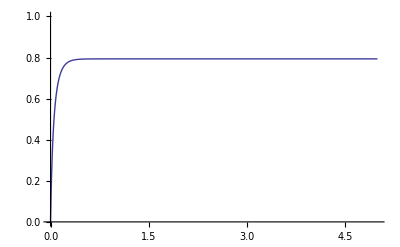

```mathematica
Plot[(-0.7934878124287316+0.7934878124287316 ⅇ^(12.369316876852979 t))/(-0.45472765611934113+1. ⅇ^(12.369316876852979 t)),{t,0,5},PlotRange->{0,1}]
```

```mathematica
Solve[(3 (1-x[t]) x'[t])/(3-x[t])^2-(3 x'[t])/(3-x[t])==-k1*((1-x[t])/((1/3)(3-x[t])))(cB0-(cA0-(1-x[t])/((1/3)(3-x[t]))))+k2*(cA0-(1-x[t])/((1/3)(3-x[t]))),x'[t]]
```

{{x'[t]→(3. (1.-(3. (1.-1. x[t]))/(3.-1. x[t]))-(18. (1.+(3. (1.-1. x[t]))/(3.-1. x[t])) (1.-1. x[t]))/(3.-1. x[t]))/((3. (1.-1. x[t]))/(3.-1. x[t])^2-3./(3.-1. x[t]))}}

```mathematica
DSolve[{D[(1-x[t])/((1/3)*(3-x[t])),t]==-k1*((1-x[t])/((1/3)(3-x[t])))(cB0-(cA0-(1-x[t])/((1/3)(3-x[t]))))+k2*(cA0-(1-x[t])/((1/3)(3-x[t]))),x[0]==0},x[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x[t]→(0.793488 (2.19912-(2.19912-2.69314×10^-16 ⅈ) 2.71828^(12.3693 t)))/(1.-(2.19912-2.69314×10^-16 ⅈ) 2.71828^(12.3693 t))}}

```mathematica
SpecialX[t_]=FullSimplify[(0.7934878124287316 (2.199118497726813-(2.199118497726813-2.6931434291868777*^-16 ⅈ) 2.718281828459045^(12.36931687685298 t)))/(1.-(2.199118497726813-2.6931434291868777*^-16 ⅈ) 2.718281828459045^(12.36931687685298 t))]
```

0.793488+1/(1.05099-(2.31125-2.83046×10^-16 ⅈ) ⅇ^(12.3693 t))

```mathematica
Eliminating the complex part for the same reason as in problem 1:
```

```mathematica
SpecialX[t_]=0.7934878124287316+1/(1.0509877084907762-(2.311246510625581) ⅇ^(12.36931687685298 t))
```

0.793488+1/(1.05099-2.31125 ⅇ^(12.3693 t))

```mathematica
xeq
```

0.768

```mathematica
SpecialX[100]
```

0.793488

```mathematica
Plot[SpecialX[t],{t,0,5},PlotRange->{0,1}]
```

-Graphics-

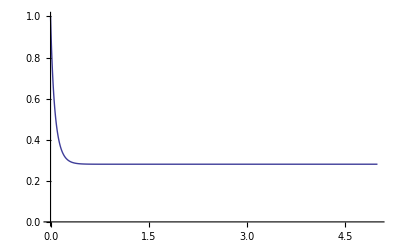

```mathematica
Plot[(1-SpecialX[t])/((1/3)(3-SpecialX[t])),{t,0,5},PlotRange->{0,1}]
```

```mathematica
(1-SpecialX[0])/((1/3)(3-SpecialX[0]))
```

1.

```mathematica
According to the keq expression, this should be .232.
```

```mathematica
(1-SpecialX[1])/((1/3)(3-SpecialX[1]))
```

0.280779

```mathematica
(1-SpecialX[3])/((1/3)(3-SpecialX[3]))
```

0.280776

```mathematica
Double-checking the initial concentration of B:
```

```mathematica
cB0-(cA0-(1-SpecialX[0])/((1/3)(3-SpecialX[0])))
```

2.

```mathematica
Observing the equilibrium concentration of B:
```

```mathematica
cB0-(cA0-(1-SpecialX[10])/((1/3)(3-SpecialX[10])))
```

1.28078

```mathematica
Double-checking the initial concentration of C:
```

```mathematica
(cA0-(1-SpecialX[0])/((1/3)(3-SpecialX[0])))
```

0.

```mathematica
Observing the equilibrium concentration of C:
```

```mathematica
(cA0-(1-SpecialX[10])/((1/3)(3-SpecialX[10])))
```

0.719224

```mathematica
There is a disagreement (ca. 5%) between the kinetic diff eq and the equilibrium expression. This is true when Mathematica's DSolve and Separation then Integration methods are used.
```

```mathematica
Redefining the  number of moles as a function of time:
```

```mathematica
nmol[x_]=1-x+2-x+x
```

```mathematica
nmol2[t_]=3-SpecialX[t]
```

2.20651-1/(1.05099-2.31125 ⅇ^(12.3693 t))

```mathematica
Redefining the volume as a function of time, invoking the number of moles as a function of time:
```

```mathematica
Vol[t_]=(1/3)*(3-SpecialX[t])
```

1/3 (2.20651-1/(1.05099-2.31125 ⅇ^(12.3693 t)))

```mathematica
Re[Vol[0]]
```

1.

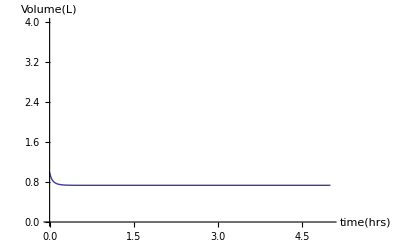

```mathematica
Plot[Vol[t],{t,0,5},PlotRange->{0,4},AxesLabel->{"time(hrs)","Volume(L)"}]
```

```mathematica
As expected, the volume starts off at 1 and decreases.  In the equilibrium limit the volume of the system is:
```

```mathematica
Vol[5] (* Liters *)
```

0.735504

```mathematica
(1-SpecialX[5])/Vol[5]
```

0.280776

```mathematica
Problem 3:
```

```mathematica
Clear[k1,k2,k3,cA,cB,cC]
```

```mathematica
ChemicalData["Acetaldehyde","MoleculePlot"]
```

-Graphics3D-

```mathematica
Assume elementry reaction kinetics for each of the four sub-reactions.  Furthermore, it is assumed that initially there  only species present is acetaldehyde and no other reactant or product.  This reaction is expected to be of shifting order.  Meaning that the relative disappearance of acetaldehyde will be modeled well for one type of rate expression at small t and another for larger t.
```

```mathematica
Let acetaldehyde be referred to as Ac, the methyl radical be referred to as Me, and the CHO radical as ChO.
```

```mathematica
Part A:
```

```mathematica
The rate of change in the concentration of Ac will be given by:
```

```mathematica
Subscript[dc, Ac]/dt=-Subscript[k, 1]*Subscript[c, Ac]-Subscript[k, 2]*Subscript[c, Ac] Subscript[c, Me]-Subscript[k, 3]*Subscript[c, Ac] Subscript[c, ChO]
```

```mathematica
The rate of change in the concentration of Me will be given by:
```

```mathematica
Subscript[dc, Me]/dt=-Subscript[k, 1]*Subscript[c, Ac]-Subscript[k, 2]*Subscript[c, Ac] Subscript[c, Me]+Subscript[k, 2]*Subscript[c, Ac] Subscript[c, Me]-Subscript[k, 3]*Subscript[c, Ac] Subscript[c, ChO]+Subscript[k, 3]*Subscript[c, Ac] Subscript[c, ChO]-2 Subscript[k, 4]*Subscript[c, Me]^2
```

```mathematica
This simplifies to:
```

```mathematica
Subscript[dc, Me]/dt=-Subscript[k, 1]*Subscript[c, Ac]-2 Subscript[k, 4]*Subscript[c, Me]^2
```

```mathematica
The rate of change in the concentration of ChO will be given by:
```

```mathematica
Subscript[dc, ChO]/dt=Subscript[k, 1]*Subscript[c, Ac]-Subscript[k, 3]*Subscript[c, Ac] Subscript[c, ChO]
```

```mathematica
Part B:
```

```mathematica
To obtain a rate of change expression for the disappearance of acetaldehyde which reduces to (Subscript[c, Ac])^(3/2), first assume a pseudo-steady-state.  Therefore, the left-hand-side of each rate expression goes to zero.
```

```mathematica
0=-Subscript[k, 1]*Subscript[c, Ac]-Subscript[k, 2]*Subscript[c, Ac] Subscript[c, Me]-Subscript[k, 3]*Subscript[c, Ac] Subscript[c, ChO]
```

```mathematica
0=-Subscript[k, 1]*Subscript[c, Ac]-2 Subscript[k, 4]*Subscript[c, Me]^2
```

```mathematica
0=Subscript[k, 1]*Subscript[c, Ac]-Subscript[k, 3]*Subscript[c, Ac] Subscript[c, ChO]
```

```mathematica
Rearrange the latter two to solve for Subscript[c, Me] and Subscript[c, ChO] in terms of Subscript[c, Ac].
```

```mathematica
Solve[0==Subscript[k, 1]*Subscript[c, Ac]-2 Subscript[k, 4]*Subscript[c, Me]^2,Subscript[c, Me]]
```

{{c_Me→-(√c_Ac √k_1)/(√2 √k_4)},{c_Me→(√c_Ac √k_1)/(√2 √k_4)}}

```mathematica
The negative solution is ignored.
```

```mathematica
Solve[0==Subscript[k, 1]*Subscript[c, Ac]-Subscript[k, 3]*Subscript[c, Ac] Subscript[c, ChO],Subscript[c, ChO]]
```

{{c_ChO→k_1/k_3}}

```mathematica
Substitution of these expressions into the rate of change in Subscript[c, Ac]  becomes:
```

```mathematica
Subscript[dc, Ac]/dt=-Subscript[k, 1]*Subscript[c, Ac]-Subscript[k, 2]*Subscript[c, Ac]((√Subscript[c, Ac] √Subscript[k, 1])/(√2 √Subscript[k, 4]))-Subscript[k, 3]*Subscript[c, Ac](Subscript[k, 1]/Subscript[k, 3]);
```

Set::write: Tag Times in dc_Ac/dt is Protected.

```mathematica
Simplify[-Subscript[k, 1]*Subscript[c, Ac]-Subscript[k, 2]*Subscript[c, Ac]((√Subscript[c, Ac] √Subscript[k, 1])/(√2 √Subscript[k, 4]))-Subscript[k, 3]*Subscript[c, Ac](Subscript[k, 1]/Subscript[k, 3])]
```

-2 c_Ac k_1-(c_Ac^(3/2) √k_1 k_2)/(√2 √k_4)

```mathematica
If Subscript[k, 2]/(√(2 Subscript[k, 4]))is large relative to 2*Subscript[k, 1], then the first term can be neglected and
```

```mathematica
Subscript[dc, Ac]/dt=-(Subscript[c, Ac]^(3/2) √Subscript[k, 1] Subscript[k, 2])/(√2 √Subscript[k, 4])
```

```mathematica
Problem 4:
```

```mathematica
The general approach to this problem is to write out various reaction mechanisms and perform an analysis simmilar to Problem 3.  Proceed to eliminate mechanisms until the mechanism suggests kinetics that agree with experimentally determined parameters.  Note: It is impossible to prove that a mechanism is correct.  Rather the mechanism will have implications that agree (are consistent)or disagree with experimentally determined analyses.
```

```mathematica
If the mechanism were a two-step process like:
```

```mathematica
A+B(->)^Subscript[k, 1] AB
```

```mathematica
AB(->)^Subscript[k, 2] Subscript[A, 2] B
```

```mathematica
Assuming that each step is an  irreversible,elementry reaction would lead to the following rate expressions:
```

```mathematica
Subscript[dc, A]/dt=-Subscript[k, 1]*Subscript[c, A]*Subscript[c, B]-Subscript[k, 2]*Subscript[c, A] Subscript[c, AB]
```

```mathematica
Subscript[dc, AB]/dt=Subscript[k, 1]*Subscript[c, A] Subscript[c, B]-Subscript[k, 2]*Subscript[c, A]*Subscript[c, AB]
```

```mathematica
Subscript[dc, Subscript[A, 2] B]/dt=Subscript[k, 2]*Subscript[c, A] Subscript[c, AB]
```

```mathematica
Make the pseudo-steady-state approximation.
```

```mathematica
0=-Subscript[k, 1]*Subscript[c, A]*Subscript[c, B]-Subscript[k, 2]*Subscript[c, A] Subscript[c, AB]
```

```mathematica
0=Subscript[k, 1]*Subscript[c, A] Subscript[c, B]-Subscript[k, 2]*Subscript[c, A]*Subscript[c, AB]
```

```mathematica
0=Subscript[k, 2]*Subscript[c, A] Subscript[c, AB]
```

```mathematica
Rearranging the second expression gives.
```

```mathematica
Solve[0==Subscript[k, 1]*Subscript[c, A] Subscript[c, B]-Subscript[k, 2]*Subscript[c, A]*Subscript[c, AB],Subscript[c, AB]]
```

{{c_AB→(c_B k_1)/k_2}}

```mathematica
Substitution into the third equation gives:
```

```mathematica
Subscript[dc, Subscript[A, 2] B]/dt=Subscript[k, 2]*Subscript[c, A](Subscript[c, B] Subscript[k, 1])/Subscript[k, 2]
```

```mathematica
Simplification yeilds the appropriate result:
```

```mathematica
Subscript[dc, Subscript[A, 2] B]/dt=Subscript[c, A] Subscript[c, B] Subscript[k, 1]
```

```mathematica
In this type of reaction, the rate-determining step is the second step and approxamately equal to the k given in the problem statement.
```